```mathematica
Z[t_]:={t,xp[t],yp[t],zp[t]}
```

```mathematica
X[t_]:={t,x,y,z}
```

```mathematica
V={ω,xp'[t],yp'[t],zp'[t]};
```

```mathematica
Ψ[x_,y_,z_]:=1/Sqrt[x^2+y^2+z^2]
```

```mathematica
γ[vx_,vy_,vz_]:=1/Sqrt[1-(vx^2+vy^2+vz^2)]
```

```mathematica
B[vx_,vy_,vz_]:=({{γ[vx,vy,vz], -γ[vx,vy,vz]*vx, -γ[vx,vy,vz]*vy, -γ[vx,vy,vz]*vz}, {-γ[vx,vy,vz]*vx, 1+(γ[vx,vy,vz]-1)vx^2/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vx*vy)/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vx*vz)/(vx^2+vy^2+vz^2)}, {-γ[vx,vy,vz]*vy, (γ[vx,vy,vz]-1)(vx*vy)/(vx^2+vy^2+vz^2), 1+(γ[vx,vy,vz]-1)vy^2/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vy*vz)/(vx^2+vy^2+vz^2)}, {-γ[vx,vy,vz]*vz, (γ[vx,vy,vz]-1)(vx*vz)/(vx^2+vy^2+vz^2), (γ[vx,vy,vz]-1)(vy*vz)/(vx^2+vy^2+vz^2), 1+(γ[vx,vy,vz]-1)vz^2/(vx^2+vy^2+vz^2)}})
```

```mathematica
BB=B[-V[[2]],-V[[3]],-V[[4]]];
pos={0,x-xp[t],y-yp[t],z-zp[t]};
BP=BB.pos;
```

```mathematica
Φ=Ψ[BP[[2]],BP[[3]],BP[[4]]];
Π = D[Φ,t]//FullSimplify;
Ψx=D[Φ,x];
Π/.{x->1/10,y->2/10,z->3/10, 
xp[t]->6/10,yp[t]->6/10,zp[t]->6/10,
xp'[t]->1/10,yp'[t]->2/10,zp'[t]->3/10, 
xp''[t]->0,yp''[t]->0,zp''[t]->0}//N
Ψx/.{t->0,x->1/10,y->2/10,z->3/10, 
xp[t]->6/10,yp[t]->6/10,zp[t]->6/10,
xp'[t]->1/10,yp'[t]->2/10,zp'[t]->3/10(*, 
xp''[t]->0,yp''[t]->0,zp''[t]->0*)}//N
Φ/.{t->0,x->1/10,y->2/10,z->3/10, 
xp[t]->6/10,yp[t]->6/10,zp[t]->6/10,
xp'[t]->1/10,yp'[t]->2/10,zp'[t]->3/10 
(*xp''[t]->0,*)(*yp''[t]->0,zp''[t]->0*)}//N
```

-0.616574

1.26678

1.34077

```mathematica
Π=Π/.{xp[t]->xp, yp[t]->yp,zp[t]->zp, xp'[t]->vx, yp'[t]->vy, zp'[t]->vz, xp''[t]->ax, yp''[t]->ay,zp''[t]->az,t->0}//FullSimplify
```

((vx (x-xp)+vy (y-yp)+vz (z-zp)) ((-1+vz^2) (-1+ax (x-xp)+ay (y-yp))+vy^2 (-1+ax (x-xp)+az (z-zp))+vx^2 (-1+ay (y-yp)+az (z-zp))+az (-z+zp)+vy vz (az (-y+yp)+ay (-z+zp))+vx (ay vy (-x+xp)+az vz (-x+xp)+ax vy (-y+yp)+ax vz (-z+zp))) √(-1/(-1+vx^2+vy^2+vz^2)(x^2-(-1+vy^2+vz^2) xp^2+y^2-vz^2 (x^2+(y-yp)^2)-2 y yp+yp^2+z^2-vy (2 vx x (-y+yp)+vy (x^2+(z-zp)^2))-vx^2 ((y-yp)^2+(z-zp)^2)+2 vz (vx x+vy (y-yp)) (z-zp)-2 z zp+zp^2+2 xp ((-1+vy^2+vz^2) x+vx vy (-y+yp)+vx vz (-z+zp)))))/(x^2-(-1+vy^2+vz^2) xp^2+y^2-vz^2 (x^2+(y-yp)^2)-2 y yp+yp^2+z^2-vy (2 vx x (-y+yp)+vy (x^2+(z-zp)^2))-vx^2 ((y-yp)^2+(z-zp)^2)+2 vz (vx x+vy (y-yp)) (z-zp)-2 z zp+zp^2+2 xp ((-1+vy^2+vz^2) x+vx vy (-y+yp)+vx vz (-z+zp)))^2

```mathematica
Π/.{
xp->6/10,yp->6/10,zp->6/10,
vx->1/10,vy->2/10,vz->3/10,
ax->0,ay->0,az->0}//FullSimplify
```

(250 √86 (-18+5 x+10 y+15 z))/((2646+2175 x^2+30 y (-98+75 y)+60 (-52+5 y) z+2375 z^2+10 x (-276+10 y+15 z))^(3/2))

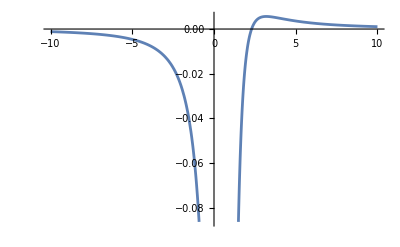

```mathematica
Plot[Π/.{x->xx,y->2/10,z->3/10,
xp->6/10,yp->6/10,zp->6/10,
vx->1/10,vy->2/10,vz->3/10,
ax->0,ay->0,az->0},{xx,-10,10}]
```

```mathematica
Integrate[r^2(250 √86 (-18+5 x+10 y+15 z))/((2646+2175 x^2+30 y (-98+75 y)+60 (-52+5 y) z+2375 z^2+10 x (-276+10 y+15 z))^(3/2)),{r,0,h}]
```

-((18000 √43)/(5292-6240 r Cos[f]+6925 r^2 Cos[f]^2-2175 r^2 Cos[f]^2 Cos[2 th]-5520 r Cos[f] Sin[th]+300 r^2 Cos[f]^2 Sin[th]-5880 r Sin[f] Sin[th]+600 r^2 Cos[f] Sin[f] Sin[th]+4500 r^2 Sin[f]^2 Sin[th]^2+100 r^2 Sin[2 f] Sin[th]^2)^(3/2))+(15000 √43 r Cos[f])/(5292-6240 r Cos[f]+6925 r^2 Cos[f]^2-2175 r^2 Cos[f]^2 Cos[2 th]-5520 r Cos[f] Sin[th]+300 r^2 Cos[f]^2 Sin[th]-5880 r Sin[f] Sin[th]+600 r^2 Cos[f] Sin[f] Sin[th]+4500 r^2 Sin[f]^2 Sin[th]^2+100 r^2 Sin[2 f] Sin[th]^2)^(3/2)+(5000 √43 r Cos[f] Sin[th])/(5292-6240 r Cos[f]+6925 r^2 Cos[f]^2-2175 r^2 Cos[f]^2 Cos[2 th]-5520 r Cos[f] Sin[th]+300 r^2 Cos[f]^2 Sin[th]-5880 r Sin[f] Sin[th]+600 r^2 Cos[f] Sin[f] Sin[th]+4500 r^2 Sin[f]^2 Sin[th]^2+100 r^2 Sin[2 f] Sin[th]^2)^(3/2)+(10000 √43 r Sin[f] Sin[th])/(5292-6240 r Cos[f]+6925 r^2 Cos[f]^2-2175 r^2 Cos[f]^2 Cos[2 th]-5520 r Cos[f] Sin[th]+300 r^2 Cos[f]^2 Sin[th]-5880 r Sin[f] Sin[th]+600 r^2 Cos[f] Sin[f] Sin[th]+4500 r^2 Sin[f]^2 Sin[th]^2+100 r^2 Sin[2 f] Sin[th]^2)^(3/2)

```mathematica
x= r Sin[th]Cos[f];
y=r Sin[th]Sin[f];
z=r Cos[f];
```